## A general formula for analog low-pass Butterworth filters: Problem 5.1

```mathematica
Clear["Global`*"];butterworth[ω_,n_?OddQ]:=TransferFunctionModel[ω/(s+ω)∏_(i=1)^((n-1)/2) ω^2/(s^2+2Cos[(π i)/n]ω s+ω^2),s]
butterworth[ω_,n_]:=TransferFunctionModel[∏_(i=1)^(n/2) ω^2/(s^2+2Cos[(π (i-1/2))/n]ω s+ω^2),s]
```

```mathematica
butterworth[Subscript[ω, N],2]
```

ω_N^2/(s^2+√2 s ω_N+ω_N^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

A third-order Butterworth filter :

```mathematica
Butter3 =butterworth[1,3]
```

1/((1+s) (1+s+s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Butter3Out = OutputResponse[Butter3,UnitStep[t],t]
```

{1/3 ⅇ^-t (-3+3 ⅇ^t-2 √3 ⅇ^(t/2) Sin[(√3 t)/2]) UnitStep[(√3 t)/2]}

A third-order Bessel filter :

```mathematica
Bessel3 = TransferFunctionModel[15/(s^3+6. s^2+15 s+15),s];
```

```mathematica
Bessel3Out = OutputResponse[Bessel3,UnitStep[t],t];
```

Graph the frequency and step responses:

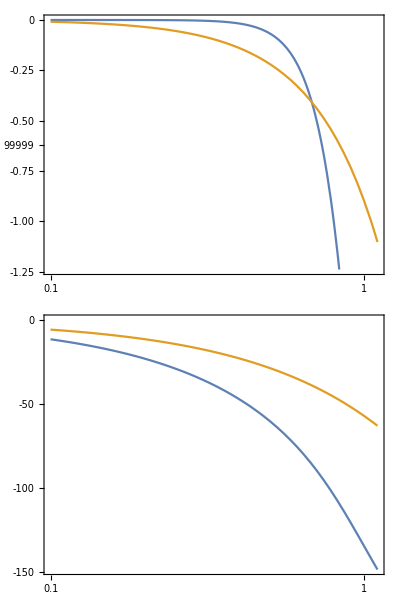

```mathematica
BodePlot[{Butter3,Bessel3},{.1,1.1}]
```

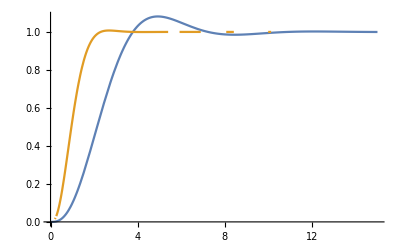

```mathematica
Plot[{Butter3Out,Bessel3Out},{t,0,15},PlotRange->All]
```

Repeat for n=2:

```mathematica
Butter2 =butterworth[1,2]
```

1/(1+√2 s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Bessel2 = TransferFunctionModel[1/(s^2+√3 s+1),s];
```

```mathematica
Butter2Out = OutputResponse[Butter2,UnitStep[t],t] // Simplify
```

{(1/2+ⅈ/2) ((1-ⅈ)-ⅇ^(-((1+ⅈ) t)/(√2))+ⅈ ⅇ^(-((1-ⅈ) t)/(√2))) UnitStep[t]}

```mathematica
Bessel2Out = OutputResponse[Bessel2,UnitStep[t],t] // Simplify
```

{1/2 ⅇ^(-1/2 (ⅈ+√3) t) (-1-ⅈ √3+ⅈ (ⅈ+√3) ⅇ^(ⅈ t)+2 ⅇ^(1/2 (ⅈ+√3) t)) UnitStep[t]}

```mathematica
naive2= TransferFunctionModel[1/(1+s)^2,s];
naive2out=OutputResponse[naive2,UnitStep[t],t] // Simplify
```

{ⅇ^-t (-1+ⅇ^t-t) UnitStep[t]}

```mathematica
gen2= TransferFunctionModel[1/(1+2ζ s + s^2),s];
gen2out=OutputResponse[gen2,UnitStep[t],t] ;
FullSimplify[gen2out, Assumptions-> 0<ζ<1]
```

{1/(2 (-1+ζ^2))ⅇ^(-t (ζ+ⅈ √(1-ζ^2))) (1-ζ^2+ⅈ ζ √(1-ζ^2)+2 ⅇ^(t (ζ+ⅈ √(1-ζ^2))) (-1+ζ^2)+ⅇ^(2 ⅈ t √(1-ζ^2)) (1-ζ^2-ⅈ ζ √(1-ζ^2))) UnitStep[t]}

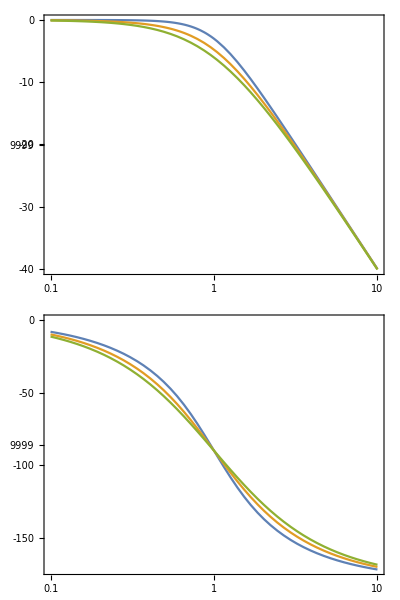

```mathematica
BodePlot[{Butter2,Bessel2,naive2},{.1,10}]
```

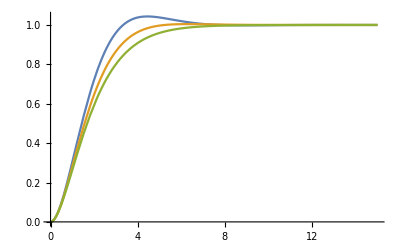

```mathematica
Plot[{Butter2Out,Bessel2Out,naive2out},{t,0,15},PlotRange->All]
```

Repeat for n=4:

```mathematica
Butter4 =butterworth[1,4] // N
```

1./((1.+0.765367 s+s^2) (1.+1.84776 s+s^2))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111.1.1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Bessel4 = TransferFunctionModel[105/(s^4+10. s^3+45 s^2+105 s+105),s];
```

```mathematica
Bessel4Out = OutputResponse[Bessel4,UnitStep[t],t];
```

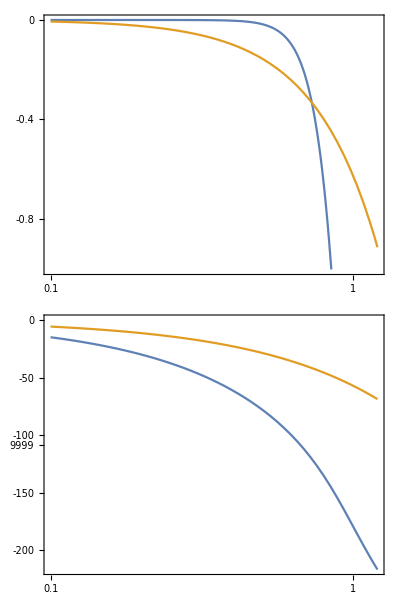

```mathematica
BodePlot[{Butter4,Bessel4},{.1,1.2}]
```

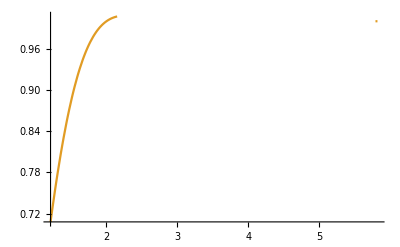

```mathematica
Plot[{Butter4Out,Bessel4Out},{t,0,15},PlotRange->All]
```

```mathematica
Butter2Mag =1/(s^2+2 ζ s+1) /. s->I ω
```

1/(1+2 ⅈ ζ ω-ω^2)

```mathematica
Conjugate[Butter2Mag]
```

1/(1-Conjugate[ω]^2-2 ⅈ Conjugate[ζ ω])

```mathematica
Series[Butter2Mag.Conjugate[Butter2Mag], {ω, 0, 3}]
```

1/(1+2 ⅈ ζ ω-ω^2).1/(1-Conjugate[ω]^2-2 ⅈ Conjugate[ζ ω])

```mathematica
Phi = ArcTan[(2ζ ω)/(1-ω^2)]
```

ArcTan[(2 ζ ω)/(1-ω^2)]

```mathematica
Series[Phi, {ω, 0, 3}]
```

2 ζ ω+1/3 (6 ζ-8 ζ^3) ω^3+O[ω]^4

Better way to look at group delay

```mathematica
n0 = 3; b3a =b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i)   (* transfer function (not formal) n=3 Bessel *)
```

b[3,0]/(b[3,0]+s b[3,1]+s^2 b[3,2]+s^3 b[3,3])

```mathematica
b3 = b3a /. s-> I ω   (* substitute s=iω for frequency response *)
```

b[3,0]/(b[3,0]+ⅈ ω b[3,1]-ω^2 b[3,2]-ⅈ ω^3 b[3,3])

```mathematica
ϕ3 =ArcTan[ Refine[Im[ ComplexExpand[b3]],Element[ω,Reals]]/Refine[Re[ ComplexExpand[b3]],Element[ω,Reals]]]// Simplify;
(* to get Im and Re --> have to tell Mathematica ω is real.... *)
```

```mathematica
d3 = -D[ϕ3,ω]  // Simplify;   (* this is the group delay *)
```

```mathematica
τ3 = Series[d3,{ω,0,9}]  ;(* now expand to lowest order to see "flat" property *)
```

```mathematica
n0 = 3; b3a =b[n0,0]/(∑_(i=0)^n0 b[n0,i] s^i)
```

b[3,0]/(b[3,0]+s b[3,1]+s^2 b[3,2]+s^3 b[3,3])